# CrossTabulate

Computes the contingency table for a two- or three-column dataset or a two- or three-column full array.

## DefinitionDefinitionDefine your function using the name you gave in the Title line above. You can add input cells and extra code to define additional input cases or prerequisites. All definitions, including dependencies, will be included in the generated resource function. This section should be evaluated before creating the Examples section below.

```mathematica
ClearAll[CrossTabulate];

SyntaxInformation[CrossTabulate] ={"Arguments"->{_,OptionsPattern[]}};

Options[CrossTabulate]={"Sparse"->False};

CrossTabulate::narr="The first argument is expected to be an array with two or three columns.
If present the third column is expected to be numerical.";

CrossTabulate[data_Dataset,opts:OptionsPattern[]]:=
Block[{colKeys},
colKeys=Normal[data[[1]]];
If[MatchQ[colKeys,_Association],
CrossTabulate[Normal[data[All,Values]],opts],
(*ElSE*)
CrossTabulate[Normal[data],opts]
]
]/;Length[Dimensions[data]]==2;

CrossTabulate[arr_?MatrixQ,opts:OptionsPattern[]]:=
Block[{idRules,t},
idRules=Table[(t=Union[arr[[All,i]]];Dispatch@Thread[t->Range[Length[t]]]),{i,Min[2,Dimensions[arr][[2]]]}];

Which[
Dimensions[arr][[2]]==2,
t={
SparseArray[Map[MapThread[Replace,{#[[1]],idRules}]->#[[2]]&,Tally[arr]]],
Normal[#][[All,1]]&/@idRules
},

Dimensions[arr][[2]]==3&&VectorQ[DeleteMissing[arr[[All,3]]],NumericQ],
t={
SparseArray[Map[MapThread[Replace,{#[[1]],idRules}]->#[[2]]&,Map[{#[[1,1;;2]],Total[#[[All,3]]]}&,GatherBy[arr,Most]]]],
Normal[#][[All,1]]&/@idRules
},

True,
Message[CrossTabulate::narr];
Return[{}]
];

If[TrueQ[OptionValue[CrossTabulate,"Sparse"]],
<|"SparseMatrix"->t[[1]],"RowNames"->t[[2,1]],"ColumnNames"->t[[2,2]]|>,
(*ELSE*)
Dataset@AssociationThread[t[[2,1]],AssociationThread[t[[2,2]],#]&/@Normal[t⟦1⟧]]
]
];
```

## Documentation

### UsageUsageDocument input usage cases by first typing an input structure, then pressing to add a brief explanation of the function’s behavior for that structure. Pressing repeatedly will create new cases as needed. Every input usage case defined above should be demonstrated explicitly here. See existing documentation pages for examples.

CrossTabulate[data]

finds the contingency table for the dataset or full array data.

### Details & OptionsDetails & OptionsGive a detailed explanation of how the function is used and configured (e.g. acceptable input types, result formats, options specifications, background information). This section may include multiple cells, bullet lists, tables, hyperlinks and additional styles/structures as needed. Add any other information that may be relevant, such as when the function was first discovered or how and why it is used within a given field. Include all relevant background or contextual information related to the function, its development, and its usage.

Additional information about usage and options.

## ExamplesExamplesDemonstrate the function’s usage, starting with the most basic use case and describing each example in a preceding text cell. Within a group, individual examples can be delimited by inserting page breaks between them (either using "[Right-click]"" ▶ ""Insert Page Break" between cells or through the menu using "Insert"" ▶ ""Page Break"). Examples should be grouped into Subsection and Subsubsection cells similarly to existing documentation pages. Here are some typical Subsection names and the types of examples they normally contain: "◼ ""Basic Examples: "most basic function usage "◼ ""Scope: "input and display conventions, standard computational attributes (e.g. threading over lists) "◼ ""Options: "available options and parameters for the function "◼ ""Applications: "standard industry or academic applications "◼ ""Properties and Relations: "how the function relates to other functions "◼ ""Possible Issues: "limitations or unexpected behavior a user might experience "◼ ""Neat Examples: "particularly interesting, unconventional, or otherwise unique usage

### Basic Examples

Find the co-occurrence of the integers [1,5] in a random table of integers with two columns:

```mathematica
CrossTabulate[RandomInteger[5,{200,2}]/.x_Integer:>ToString[x]]
```

Dataset[<>]

Here is a full array with three columns, the third column is numerical:

```mathematica
Block[{n=30},
SeedRandom[32];
sarr=Transpose[{RandomChoice[CharacterRange["A","D"],n],RandomChoice[RandomWord["CommonWords",5],n],RandomReal[100,n]}]
]
```

{{C,league,47.7068},{B,league,57.679},{C,tagliatelle,7.22497},{B,league,80.9415},{B,league,84.6982},{C,hymn,24.5806},{C,league,12.3514},{B,tagliatelle,0.862345},{D,league,28.0771},{A,atavism,58.7301},{B,hymn,37.6937},{A,league,75.052},{D,league,3.37844},{A,tagliatelle,71.9668},{C,hymn,73.5633},{C,tagliatelle,67.1295},{D,atavism,79.6514},{B,tagliatelle,69.238},{C,tagliatelle,83.2488},{B,tagliatelle,47.8905},{C,atavism,73.6239},{B,league,90.9807},{D,hymn,33.8904},{B,atavism,47.3234},{A,crampon,38.4727},{C,league,23.4564},{B,crampon,2.97541},{C,hymn,65.1189},{D,league,39.9731},{B,league,59.6135}}

Here is the contingency table of the co-occurrences of each letter and with each words found by cross tabulating over the first two columns only:

```mathematica
CrossTabulate[sarr⟦All,{1,2}⟧]
```

Dataset[<>]

Here the cross tabulation uses the third column -- for each letter-word pair the corresponding values of the third column are added:

```mathematica
CrossTabulate[sarr]
```

Dataset[<>]

### Scope

Using the option

```mathematica
MyFunction[x,y,z]
```

x y z

### Options

#### “Sparse”

The result is a dataset by default; with the option setting ”Sparse”→True the result is an association with three elements: sparse matrix with the contingency values, row names, and column names.

Here is an example:

```mathematica
Block[{n=40},
data=Transpose[{ToString/@RandomInteger[{10,20},n],ToString/@RandomInteger[{1,6},n]}]
];
```

```mathematica
res=CrossTabulate[data,"Sparse"->True]
```

<|SparseMatrix→SparseArray[…],RowNames→{10,11,12,14,15,16,17,18,19,20},ColumnNames→{1,2,3,4,5,6}|>

```mathematica
MatrixForm[res["SparseMatrix"],TableHeadings->{res["RowNames"],res["ColumnNames"]}]
```

( | 1 | 2 | 3 | 4 | 5 | 6
10 | 1 | 0 | 0 | 0 | 1 | 0
11 | 0 | 1 | 1 | 3 | 0 | 0
12 | 1 | 0 | 1 | 0 | 2 | 1
14 | 0 | 0 | 0 | 1 | 1 | 3
15 | 0 | 3 | 2 | 2 | 0 | 1
16 | 0 | 1 | 1 | 0 | 0 | 0
17 | 0 | 0 | 1 | 0 | 2 | 0
18 | 0 | 1 | 1 | 1 | 0 | 1
19 | 0 | 0 | 0 | 1 | 0 | 0
20 | 1 | 0 | 2 | 1 | 1 | 0)

### Applications

#### Plot the contingency matrix

Here is a function to plot sparse contingency tables compute with CrossTabulate:

```mathematica
CTMatrixPlot[x_Association/;(KeyExistsQ[x,"SparseMatrix"]||KeyExistsQ[x,"XTABTensor"]),opts___]:=(MatrixPlot[#1,Append[{opts},FrameLabel->{{Keys[x][[2]],None},{Keys[x][[3]],None}}]]&@@x);
```

```mathematica
CTMatrixPlot[CrossTabulate[data,"Sparse"->True]]
```

CTMatrixPlot[CrossTabulate[data,Sparse→True]]

#### Movie reviews word-sentiment analysis

Here we get movie review data:

```mathematica
movieReviewData=Flatten@*List@@@ExampleData[{"MachineLearning","MovieReview"},"Data"];
Dimensions[movieReviewData]
```

{10662,2}

Here for each movie review we make a list of word-sentiment pairs and then join them into one big list:

```mathematica
movieReviewData=Join@@Map[Thread[{DeleteStopwords[StringSplit[#⟦1⟧]],#⟦2⟧}]&,movieReviewData];
Dimensions[movieReviewData]
```

{129342,2}

Here is a sample:

```mathematica
RandomSample[movieReviewData,12]
```

{{constant,positive},{,,negative},{mix,negative},{,,negative},{match,negative},{russell,negative},{writer-director,negative},{tautou,negative},{,,positive},{surprise,positive},{,,negative},{fits,positive}}

Here we find the word-sentiment contingency table as a sparse matrix in order to plot it below:

```mathematica
cm=CrossTabulate[movieReviewData,"Sparse"->True];
```

Plot of the contingency table:

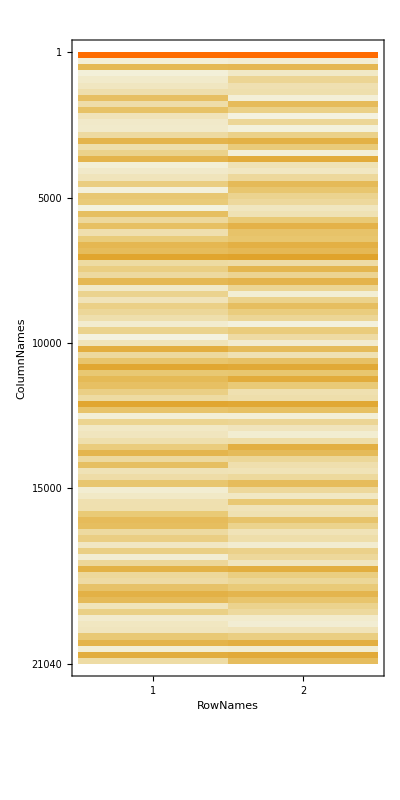

```mathematica
CTMatrixPlot[cm,AspectRatio->2]
```

Here we find the contingency table dataset:

```mathematica
ct=CrossTabulate[movieReviewData,"Sparse"->False];
```

Here we show the most prominent words for negative reviews:

```mathematica
ct[ReverseSortBy[#negative-#positive&]][1;;200,All]
```

Dataset[<>]

### Properties and Relations

### Possible Issues

### Neat Examples

```mathematica
titanic=ExampleData[{"Dataset","Titanic"}];
```

```mathematica
CrossTabulate[titanic[All,{"sex","class"}]]
```

Dataset[<>]

```mathematica
CrossTabulate[titanic[All,{"survived","sex"}]]
```

Dataset[<>]

```mathematica
CrossTabulate[titanic[All,{"survived","sex","age"}]]
```

Dataset[<>]

## Source & Additional Information

### Contributed ByContributed ByEnter the name of the person, people or organization that should be publicly credited with contributing this function.

Anton Antonov

### KeywordsKeywordsList relevant terms (e.g. functional areas, algorithm names, related concepts) that should be used to include the function in search results.

contingency table

contingency matrix

frequency distribution

### Categories

Cloud & Deployment |  Core Language & Structure
 Data Manipulation & Analysis |  Engineering Data & Computation
 External Interfaces & Connections |  Financial Data & Computation
 Geographic Data & Computation |  Geometry
 Graphs & Networks |  Higher Mathematical Computation
 Images |  Just For Fun
 Knowledge Representation & Natural Language |  Machine Learning
 Notebook Documents & Presentation |  Programming Utilities
 Repository Tools |  Scientific and Medical Data & Computation
 Social, Cultural & Linguistic Data |  Sound
 Strings & Text |  Symbolic & Numeric Computation
 System Operation & Setup |  Time-Related Computation
 User Interface Construction |  Visualization & Graphics

### Related SymbolsRelated SymbolsList up to twenty documented, system-level Wolfram Language symbols related to the function.

GroupBy

Tally

MartixPlot

MatrixForm

Dataset

ClassifierMeasurementsObject

### Related Resource ObjectsRelated Resource ObjectsList the names of published resource objects from any Wolfram repository that are related to this function.

### Source/Reference CitationSource/Reference CitationGive a bibliographic-style citation for the original source of the function and/or its components (e.g. a published paper, algorithm, or code repository).

Wikipedia entry, Contingency table

Anton Antonov, "Contingency tables creation examples", (2016), MathematicaForPrediction at WordPress.

### LinksLinksList additional URLs or hyperlinks for external information related to the function.

CrossTabulate.m

### TestsTestsSpecify an optional list of tests for verifying that the function is working properly in any environment. Tests can be specified as Input/Output cell pairs or as symbolic VerificationTest expressions for including additional options.

```mathematica
Block[{n=300},
sarr=Transpose[{RandomChoice[CharacterRange["A","D"],n],RandomChoice[RandomWord["CommonWords",5],n],ConstantArray[1,n]}]
];
CrossTabulate[data⟦All,{1,2}⟧,"Sparse"->False]==CrossTabulate[data,"Sparse"->False]
```

True

```mathematica
CrossTabulate[data⟦All,{1,2}⟧,"Sparse"->True]==CrossTabulate[data,"Sparse"->True]
```

True

```mathematica
titanic=ExampleData[{"Dataset","Titanic"}];
CrossTabulate[titanic⟦All,{1,4}⟧]==CrossTabulate[Normal[titanic[Values]]⟦All,{1,4}⟧]
```

True

```mathematica
CrossTabulate[titanic⟦All,{1,2}⟧,"Sparse"->False]==CrossTabulate[Normal[titanic[Values]]⟦All,{1,2}⟧,"Sparse"->False]
```

True

```mathematica
CrossTabulate[titanic⟦All,{3,4}⟧,"Sparse"->True]==CrossTabulate[Normal[titanic[Values]]⟦All,{3,4}⟧,"Sparse"->True]
```

True

```mathematica
titanic2=DeleteMissing[titanic,1,2][All,{"sex","class","age"}];
```

```mathematica
ct1=CrossTabulate[titanic2]
```

Dataset[<>]

```mathematica
ct2=Total/@titanic2[GroupBy[{#sex,#class}&],All,"age"]
```

Dataset[<>]

```mathematica
ct1["female","1st"]==Normal[ct2][{"female","1st"}]
```

True

```mathematica
ct1["male","3rd"]==Normal[ct2][{"male","3rd"}]
```

True

## Author Notes

The function CrossTabulate corresponds to R’s function xtabs.

## Submission NotesSubmission NotesEnter any additional information that you would like to communicate to the reviewer here. This section will not be included in the published resource.

Additional information for the reviewer.

ToExpression::esntx: Could not parse TemplateBox[«1»] as input.